# KASUS TOV SCgrav Carballo-Rubio dengan definisi λ==√(1+(2 G l^2 (m[r]+4 π r^3 p[r]))/(r^2(r-2 G m[r])))

```mathematica
Clear["Global`*"];

showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
clearStatus[]:=showStatus[""];
clearStatus[]
cek[r_,p_]:=((1+λ)^2 (l^4+l^2 r^2 (-2+λ)-r^4 (-1+λ^2)))/(4 G l^2 π r (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))+(2 r (1+λ) (-r^4 (-1+λ) (1+λ)^2+l^4 (1+2 λ)+l^2 r^2 (-2-2 λ+λ^2+λ^3)) p)/(l^2 (l^2-r^2 (1+λ)) (l^2+r^2 (-1+λ^2)))
persp:=p'[r]==cek[r,p[r]]
```

### Backward

```mathematica
G=1.323790281083862 10^-12;
ms=1.1154605324408694 10^15;
λ=10.0;
l=3.* 10.^0;(*√(10/(12π)) 1.616 10^-35;*)
r0=10.*10.^3;rn=10.^-6;
p0=-10.^-9;
```

```mathematica
s=NDSolve[{persp,p[r0]==p0,WhenEvent[r==0,{rbs=r,"StopIntegration"}]},{p},{r,r0,rn},EvaluationMonitor:>showStatus[ToString[CForm[r]]<>" , "<>ToString[CForm[p[r]]]]]
rbs
```

NDSolve::ndsz: At r == 0.904534, step size is effectively zero; singularity or stiff system suspected.

{{p→InterpolatingFunction[{{0.904534, 10000.}}, <>]}}

rbs

```mathematica
po[r_]=Evaluate[p[r]/.s][[1]];
mo[r_]=(r^3 (-1+λ^2-8 G l^2 π po[r]))/(2 G (l^2+r^2 (-1+λ^2)));
pa[r_]:=-1/(8π G r^2 r0^2)(r0^2-r^2 Exp[-((λ+1)(r0^2-r^2))/l])
```

InterpolatingFunction::dmval: Input value {0.204287} lies outside the range of data in the interpolating function. Extrapolation will be used.

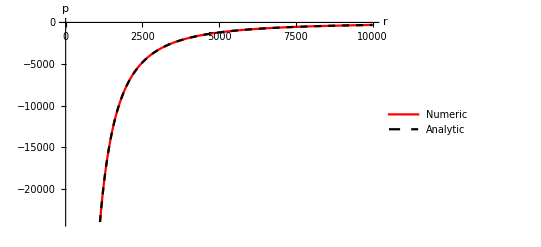

```mathematica
Plot[{pa[r],po[r]},{r,rn,r0},AxesLabel->{"r","p"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Numeric","Analytic"},PlotRange->Automatic]
```

## Forward

```mathematica
rn0=1.
po[rn0]
pa[rn0]
```

1.

-2.70055×10^23

-3.00567×10^10

```mathematica
pinit=po[rn0]
s1=NDSolve[{persp,p[rn0]==pinit,WhenEvent[{p[r]==0},{rbs=r,"StopIntegration"}]},{p},{r,rn0,r0},EvaluationMonitor:>showStatus[ToString[CForm[r]]<>" , "<>ToString[CForm[p[r]]]]]
rbs
po1[r_]=Evaluate[p[r]/.s1][[1]];
po1[rbs]>pinit
```

-2.70055×10^23

{{p→InterpolatingFunction[{{1., 5.28847}}, <>]}}

5.28847

True

```mathematica
mo1[r_]=(r^3 (-1+λ^2-8 G l^2 π po1[r]))/(2 G (l^2+r^2 (-1+λ^2)));
pa1[r_]:=-1/(8π G r^2 rbs^2)(rbs^2-r^2 Exp[-((λ+1)(rbs^2-r^2))/l])
```

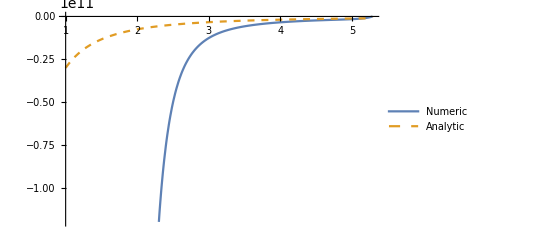

```mathematica
Plot[{po1[r],pa1[r]},{r,rn0,rbs},PlotRange->Automatic,PlotStyle->{{Thick},{Dashed}},PlotLegends->{"Numeric","Analytic"}]
```

## Hasilnya berbeda karena integrasi forward start dari daerah singular

InterpolatingFunction::dmval: Input value {0.204287} lies outside the range of data in the interpolating function. Extrapolation will be used.

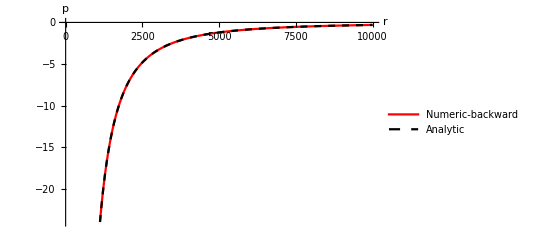

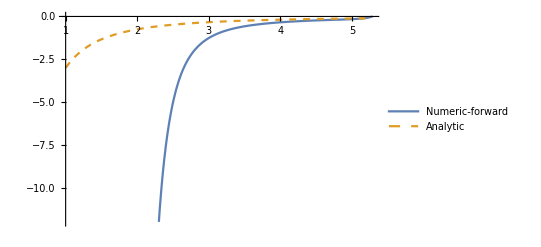

```mathematica
Plot[{pa[r]*10^-3,po[r]*10^-3},{r,rn,r0},AxesLabel->{"r","p"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Numeric-backward","Analytic"},PlotRange->Automatic]
Plot[{po1[r]*10^-10,pa1[r]*10^-10},{r,rn0,rbs},PlotRange->Automatic,PlotStyle->{{Thick},{Dashed}},PlotLegends->{"Numeric-forward","Analytic"}]
```

```mathematica
ClearAll[x]
x[i_]:=rn+i(r0-rn)/10000
data=Table[{x[i]/1000,pa[x[i]]*10^-3,po[x[i]]*10^-3},{i,0,10000}]
Export[FileNameJoin[{NotebookDirectory[],"TOV-reverse-6.0-b.dat"}],data]
```

InterpolatingFunction::dmval: Input value {1.×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{1.×10^-9,-3.00567×10^19,-2.29617×10^141},{0.001,-3.00566×10^7,-2.70023×10^20},9997,{9.999,-0.300627,-0.300627},{10.,0.,-1.×10^-12}}
 |  |  |  |

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\TOV-reverse-6.0-b.dat

```mathematica
ClearAll[x]
x[i_]:=rn0+i(rbs-rn0)/10000
data=Table[{x[i],po1[x[i]]*10^-10,pa1[x[i]]*10^-10},{i,0,10000}]
Export[FileNameJoin[{NotebookDirectory[],"TOV-reverse-6.0-f.dat"}],data]
```

{{1.,-2.70055×10^13,-3.00567},{1.00043,-2.56898×10^13,-3.00309},9997,{5.28805,-0.000594083,-0.00178995},{5.28847,-4.03821×10^-16,0.}}
 |  |  |  |

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\TOV-reverse-6.0-f.dat